```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,10}];
```

```mathematica
Model0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\Practice_Model\\Practice_Model.txt","Table"];

Model=Drop[Model0,1];
```

```mathematica
RadiusMass=Model[[All,{6,5}]];
RadiusLogTemp=Model[[All,{6,3}]];
RadiusTemp=Table[{RadiusLogTemp[[i,1]],10^RadiusLogTemp[[i,2]]},{i,1,Dimensions[RadiusLogTemp][[1]]}];
RadiusLogDens=Model[[All,{6,4}]];
RadiusDens=Table[{RadiusLogDens[[i,1]],10^RadiusLogDens[[i,2]]},{i,1,Dimensions[RadiusLogDens][[1]]}];
RadiusLogPress=Model[[All,{6,2}]];
RadiusPress=Table[{RadiusLogPress[[i,1]],10^RadiusLogPress[[i,2]]},{i,1,Dimensions[RadiusLogPress][[1]]}];
RadiusLumin=Model[[All,{6,7}]];
RadiusOpacity=Model[[All,{6,9}]];
RadiusGrav=Table[{RadiusMass[[i,1]], (G*RadiusMass[[i,2]])/RadiusMass[[i,1]]^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];
OpacityN=Interpolation[RadiusOpacity];
```

```mathematica
Rtot=Model[[1,6]]/Model[[1,20]];

RDown=0.05Rtot;
RUp=3.5*10^10;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
RadiusOpacityReduced=Select[RadiusOpacity,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
SoundSpeed[R_,z_]=√(γ P[R,z] / ρ[R,z]);
```

```mathematica
κFit0=Fit[RadiusOpacityReduced,Polinomi,q];
κFit[x_]=κFit0/.{q->x};
Show[Plot[OpacityN[r],{r,RDown,RUp}],ListPlot[RadiusOpacityReduced],Plot[κFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","κ (g^-1 cm^2)","Opacity"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
κ[R_,z_]=κFit[(R^2+z^2)^0.5];
```

```mathematica
σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
Mu=0.62;
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*κ[R,z]*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(κ[R,z]*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
Pr[R_,z_]=ν[R,z]/χ[R,z];
```

```mathematica
Plotχ=Plot[χ[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},Frame->True,FrameLabel->{"r/Rsun","χ (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
Show[LogPlot[ν[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,100}}],LogPlot[νdyn[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black,Dashed],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,100}}],LogPlot[νrad[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},PlotStyle->Directive[Black,Dotted],PlotRange->{{RDown/Rsun,RUp/Rsun},{0.1,100}}],Frame->True,FrameLabel->{"r/Rsun","ν (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
PlotPr=Plot[Pr[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,RDown/Rsun,RUp/Rsun},Frame->True,FrameLabel->{"r/Rsun","Pr"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
```

```mathematica
CaptionGeneral[{{"ν", Black, Automatic},{"ν_dyn",Black,Dashed},{"ν_rad",Black,Dotted}}];
```

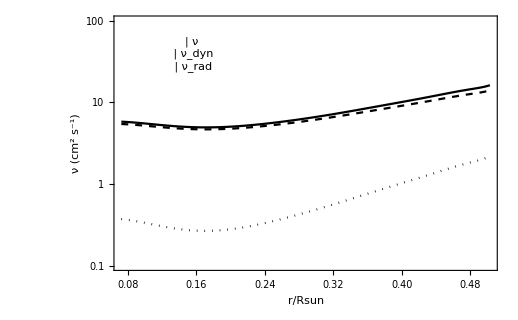
```mathematica
Plotν=-Graphics-;
```

```mathematica
Ω[R_,z_]:=√(7.4*10^-12);      dLogΩdLogr:=-2;
ldR[R_,z_]:=Ω[R,z]*R*(2+R^2/(R^2+z^2)*dLogΩdLogr);
ldz[R_,z_]:=Ω[R,z]*R*(z/(√(R^2+z^2))*dLogΩdLogr);

LastTermGS[R_,z_,kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*(kR^2+kz^2))/Ω[R,z])(PdR[R,z]-kR/kz Pdz[R,z])(kR/kz σdz[R,z]-σdR[R,z])+(2/(γ*Ω[R,z]*R))(kz^2/(kR^2+kz^2))((χ[R,z]*(kR^2+kz^2))/Ω[R,z])(ldR[R,z]-kR/kz ldz[R,z])+1/γ((χ[R,z]*(kR^2+kz^2))/Ω[R,z])((ν[R,z]*(kR^2+kz^2))/Ω[R,z])^2
```

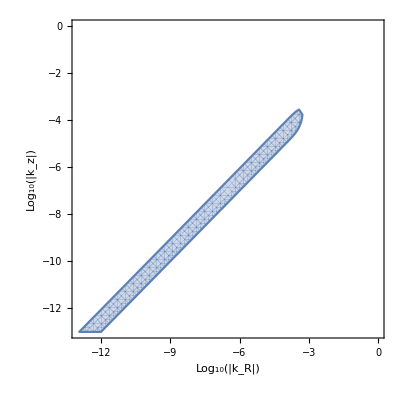
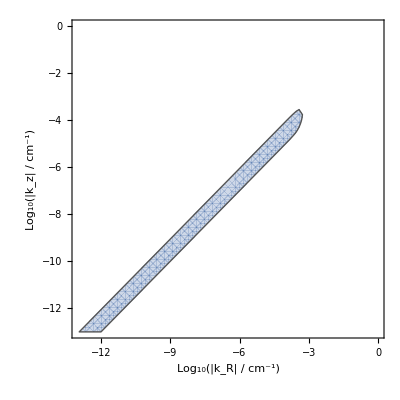
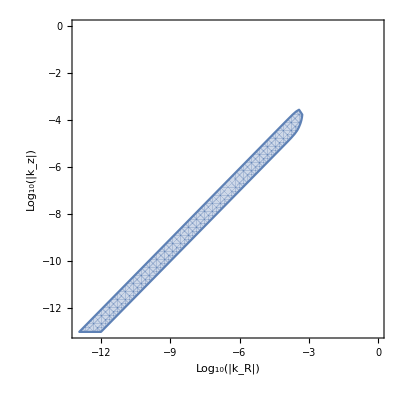
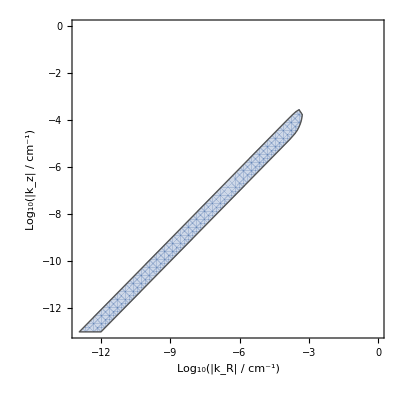
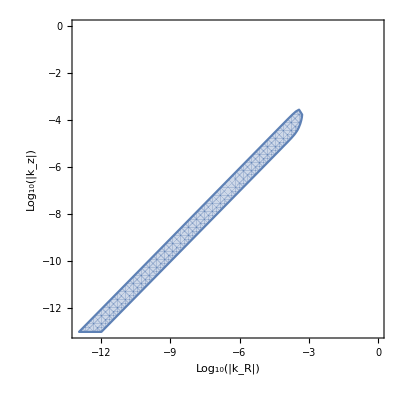
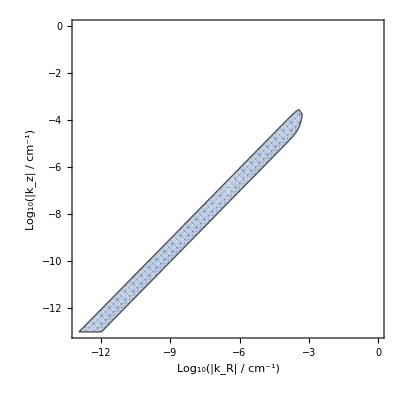
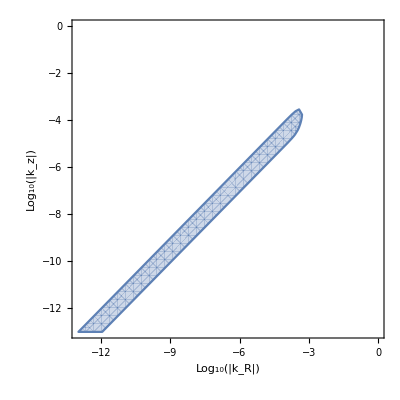
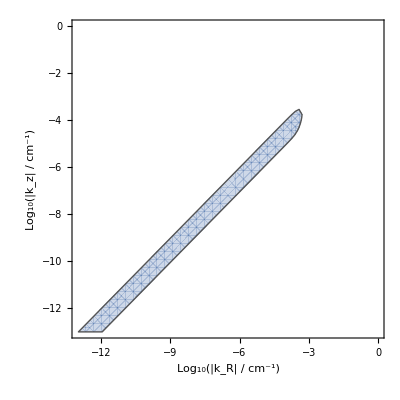
{159.75,{{(r,θ) = (0.0725933,Pi
--
36), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,Pi
--
12), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,5 Pi
----
 36), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,7 Pi
----
 36), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,Pi
--
4), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,11 Pi
-----
 36), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,13 Pi
-----
 36), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,5 Pi
----
 12), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.0725933,17 Pi
-----
 36), ν_dyn = 5.44064, ν_rad = 0.370778, Pr = 9.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.158652,Pi
--
36), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,Pi
--
12), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,5 Pi
----
 36), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,7 Pi
----
 36), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,Pi
--
4), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,11 Pi
-----
 36), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,13 Pi
-----
 36), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,5 Pi
----
 12), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.158652,17 Pi
-----
 36), ν_dyn = 4.69597, ν_rad = 0.268028, Pr = 9.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.244711,Pi
--
36), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,Pi
--
12), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,5 Pi
----
 36), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,7 Pi
----
 36), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,Pi
--
4), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,11 Pi
-----
 36), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,13 Pi
-----
 36), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,5 Pi
----
 12), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.244711,17 Pi
-----
 36), ν_dyn = 5.20313, ν_rad = 0.339804, Pr = 6.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.33077,Pi
--
36), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,Pi
--
12), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,5 Pi
----
 36), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,7 Pi
----
 36), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,Pi
--
4), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,11 Pi
-----
 36), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,13 Pi
-----
 36), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,5 Pi
----
 12), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.33077,17 Pi
-----
 36), ν_dyn = 6.89663, ν_rad = 0.60753, Pr = 4.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.416829,Pi
--
36), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,Pi
--
12), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,5 Pi
----
 36), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,7 Pi
----
 36), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,Pi
--
4), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,11 Pi
-----
 36), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,13 Pi
-----
 36), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,5 Pi
----
 12), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.416829,17 Pi
-----
 36), ν_dyn = 9.74934, ν_rad = 1.15751, Pr = 2.5*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{(r,θ) = (0.502888,Pi
--
36), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,Pi
--
12), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,5 Pi
----
 36), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,7 Pi
----
 36), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,Pi
--
4), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,11 Pi
-----
 36), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,13 Pi
-----
 36), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,5 Pi
----
 12), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,(r,θ) = (0.502888,17 Pi
-----
 36), ν_dyn = 14.0737, ν_rad = 2.20237, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-}}}

```mathematica
δR=(RUp-RDown)/5;

Timing[Table[
Rper=rper*Sin[θper];   zper=rper*Cos[θper];


"(r,θ) = (" <> ToString[rper/Rsun] <> "," <> ToString[θper]  <>"), ν_dyn = "<>ToString[νdyn[Rper,zper]] <> ", ν_rad = " <> ToString[νrad[Rper,zper]] <> (*", ξ_rad = " <> ToString[ScientificForm[χ[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> *)", Pr = " <> ToString[ScientificForm[ν[Rper,zper]/χ[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> "."

RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}],{rper,RDown,RUp,δR},{θper,π/36,17*π/36,2*π/36}]]
```